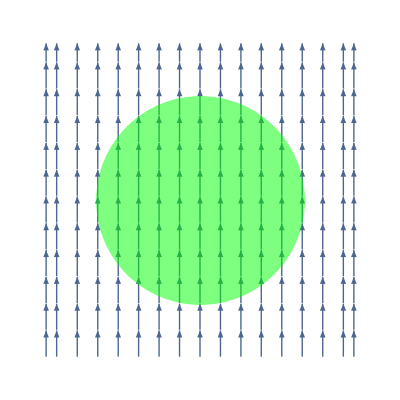

```mathematica
Show[ StreamPlot[{0,1}, {x,-1.5,1.5},{z,-1.5,1.5}, StreamStyle->Thick, Frame->False],
	Graphics[{Green,Opacity[.5], Disk[{0,0},1]}]]
```

{(3 x z)/((x^2+z^2)^(5/2)),-x^2/((x^2+z^2)^(5/2))+(2 z^2)/((x^2+z^2)^(5/2))}

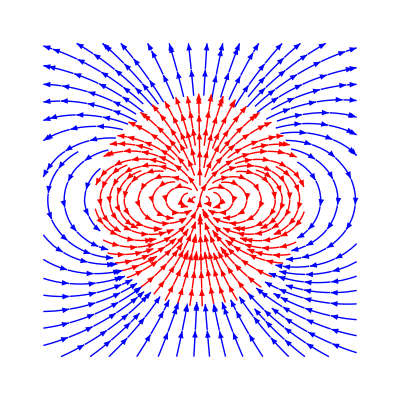

```mathematica
Vs=(p  Cos[θ])/r^2;
Es=-Grad[Vs,{r,θ,φ},"Spherical"];
Ec=TransformedField["Spherical"->"Cartesian",Es,{r,θ,φ}->{x,y,z}]/.p-> 1/.y-> 0;
Ec = {Ec[[1]],Ec[[3]]}
StreamPlot[Ec,{x,z}∈Disk[{0,0},1],StreamStyle->{Red,Thick} ];
StreamPlot[Ec,{x,-1.5,1.5}, {z,-1.5,1.5},StreamStyle->{Blue,Thick},RegionFunction->Function[{x,z},x^2+z^2>1] ];
Show[%,%%,Frame->False]
```

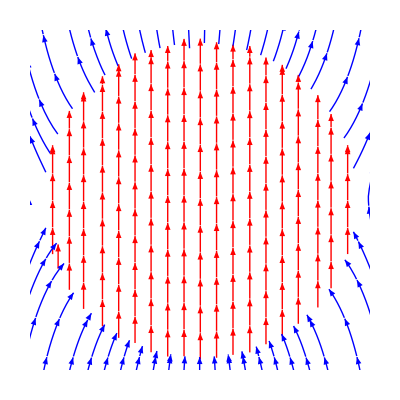

```mathematica
StreamPlot[Ec+{0,2},{x,-1.5,1.5}, {z,-1.5,1.5},StreamStyle->{Blue,Thick},RegionFunction->Function[{x,z},x^2+z^2>1] ];
StreamPlot[{0,1},{x,z}∈Disk[{0,0},1],StreamStyle->{Red,Thick} ];
Show[%,%%,Frame->False]
```

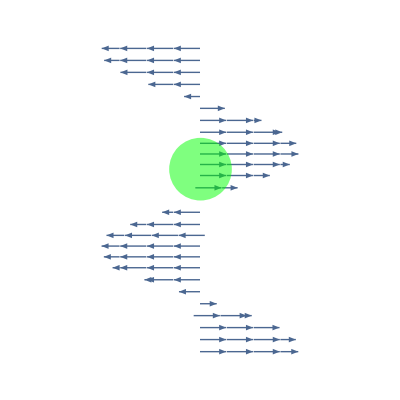

```mathematica
Show[ StreamPlot[{ Sin[z],0}, {x,-5,5},{z,-5,5},StreamStyle->{Thick},RegionFunction->Function[{x,z}, x^2≤10 Sin[z]^2 && Sign[Sin[z]]==  Sign[Sin[x]]], StreamPoints->Fine , StreamStyle->Thick, Frame->False],
	Graphics[{Green,Opacity[.5], Disk[{0,1},1]}]]
```